```mathematica
SetDirectory@NotebookDirectory[];
Import["path to QuESTlink.m"];
CreateLocalQuESTEnv["path to quest_link"];
(*Read the paper [Tyson Jones and Simon Benjamin, arXiv:1912.07904] for how to setup the environment.*)
```

## Parameters

```mathematica
numQb=10;
PI=N[π,12];
```

## QC

```mathematica
ψIN=CreateQureg[numQb];
ψOUT=CreateQureg[numQb];
ψWP=CreateQureg[numQb];
```

## Basis

```mathematica
States=Table[{},{nN,1,2^(numQb/2)}];
Do[(
B=IntegerDigits[n-1,2,numQb];
circ=Table[If[B[[k+1]]==1,Subscript[X, k],Subscript[Z, k]],{k,0,numQb-1,1}];
ApplyCircuit[circ,ψIN,ψOUT];
OUT=Round[Abs[GetQuregMatrix[ψOUT]]];
index=Position[OUT,1][[1,1]];

BN=Table[B[[k+1]],{k,0,numQb-1,2}];
nN=FromDigits[BN,2]+1;
AppendTo[States[[nN]],index];
),{n,1,2^numQb}];
States;
```

```mathematica
ProNeurons[OUT_]:=(
Pro=Table[
P=0;
Do[P=P+OUT[[States[[i,j]]]],{j,1,2^(numQb/2)}];
P
,{i,1,2^(numQb/2)}];
Return[Pro]
)
```

## Neural Network Cirucit

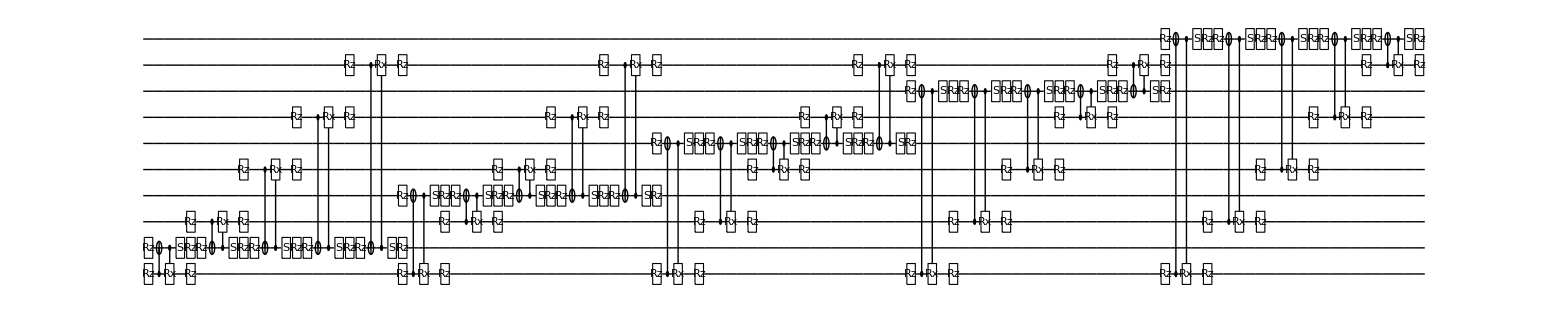

```mathematica
circuitNN[θlist_]:=(
circNN={};
Do[(
j=(b+1)/2;
Do[(
i=(a+2)/2;
θ=θlist[[numQb/2*(j-1)+i]];
circMR={Subscript[Rz, a][θ],Subscript[Rz, b][θ],Subscript[C, a][Subscript[X, b]],Subscript[C, b][Subscript[Rx, a][PI-2θ]],Subscript[S, b],Subscript[Rz, b][-θ],Subscript[Rz, a][-θ]};
circNN=Join[circNN,circMR];
),{a,0,numQb-1,2}]
),{b,1,numQb-1,2}];
Return[circNN]
)
circNN=circuitNN[Table[i/100,{i,1,(numQb/2)^2}]];
DrawCircuit@circNN
```

## Distance

-Graphics-

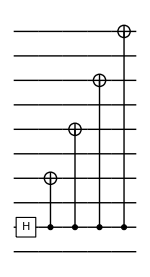

-Graphics-

```mathematica
circNeurons=Table[Subscript[H, i],{i,0,numQb-1,2}];
DrawCircuit@circNeurons
circGHZ={Subscript[H, 1]};Do[AppendTo[circGHZ,Subscript[C, 1][Subscript[X, i]]],{i,3,numQb-1,2}];
DrawCircuit@circGHZ
circPLUS=Table[Subscript[H, i],{i,1,numQb-1,2}];
DrawCircuit@circPLUS
```

```mathematica
Clear[Distance]
Distance[θlist_/;(And@@(NumericQ/@θlist))]:=(
circNN=circuitNN[θlist];

circ=Join[circNeurons,circGHZ,circNN];
ApplyCircuit[circ,ψIN,ψOUT];
OUT=Abs[GetQuregMatrix[ψOUT]]^2;
ProGHZ=ProNeurons[OUT];

circ=Join[circNeurons,circPLUS,circNN];
ApplyCircuit[circ,ψIN,ψOUT];
OUT=Abs[GetQuregMatrix[ψOUT]]^2;
ProPLUS=ProNeurons[OUT];

Dis=Total[Abs[ProGHZ-ProPLUS]]/2;

Return[Dis]
)
Distance[Table[0,{i,1,(numQb/2)^2}]]
ProGHZ
ProPLUS
```

0.9375

{0.5,1.21855×10^-32,2.8116×10^-65,6.3261×10^-65,2.63545×10^-98,1.31773×10^-98,1.05418×10^-97,6.58863×10^-98,4.94068×10^-131,1.38912×10^-194,2.77824×10^-195,1.85246×10^-163,9.88136×10^-131,4.94068×10^-131,7.40984×10^-163,4.94068×10^-131,0.5,1.21855×10^-32,2.8116×10^-65,6.3261×10^-65,2.63545×10^-98,1.31773×10^-98,1.05418×10^-97,6.58863×10^-98,4.94068×10^-131,1.38912×10^-194,2.77824×10^-195,1.85246×10^-163,9.88136×10^-131,4.94068×10^-131,7.40984×10^-163,4.94068×10^-131}

{0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125,0.03125}

## Find

Sometimes the optimisation fails, which seems to be an issue caused by a bad random seed. Just try again.

{0.947924,{0_1→-0.131213,0_2→-0.051581,0_3→-0.0006122,0_4→4.32983×10^-10,0_5→1.60807×10^-7,0_6→-0.17519,0_7→-0.237194,0_8→-0.0601288,0_9→-0.000467259,0_10→-2.71753×10^-10,0_11→0.0395095,0_12→0.463639,0_13→-0.0154706,0_14→-0.120304,0_15→-0.000754139,0_16→0.341103,0_17→0.356955,0_18→0.271457,0_19→0.254244,0_20→-0.116952,0_21→-0.0774029,0_22→1.12861,0_23→0.645092,0_24→-0.436512,0_25→0.185902}}

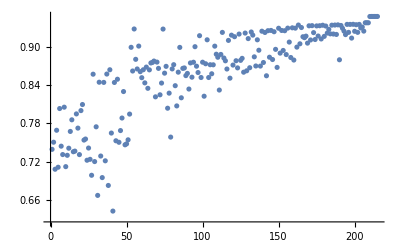

```mathematica
θlist=Table[Subscript[θ, i],{i,1,(numQb/2)^2}];
{res,data}=Reap[NMaximize[Distance[θlist],θlist,EvaluationMonitor:>Sow[Distance[θlist]]]];
res
plot=ListPlot[data]
```

## Optimal Parameters

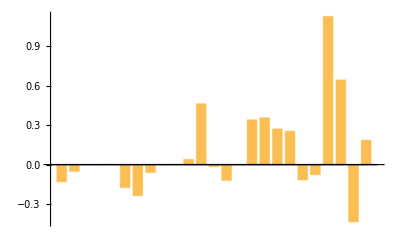

0.947924

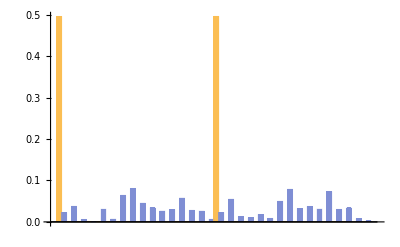

```mathematica
plotθlist=BarChart[θlist/.Last[res]]
Distance[θlist/.Last[res]]
ProGP=Table[{ProGHZ[[i]],ProPLUS[[i]]},{i,1,2^(numQb/2)}];
plotPro=BarChart[ProGP]
```

## Data and Plot

```mathematica
file=File["Ising_find_reduced.dat"];
toFile={};
AppendTo[toFile,"Optimal distance:"];
AppendTo[toFile,res[[1]]];
AppendTo[toFile,""];
AppendTo[toFile,"Optimal parameters:"];
AppendTo[toFile,θlist/.Last[res]];
AppendTo[toFile,""];
AppendTo[toFile,"Evaluations:"];
AppendTo[toFile,data];
AppendTo[toFile,""];
Export[file,toFile];
```

```mathematica
DisC=N[2(1/2-1/2^(numQb/2))+(2^(numQb/2)-2)/2^(numQb/2),12]/2
Fid=N[(1/(√2))^(numQb/2-1),12]
DisQ=N[√(1-Fid^2),12]
```

0.9375

0.25

0.968245836552

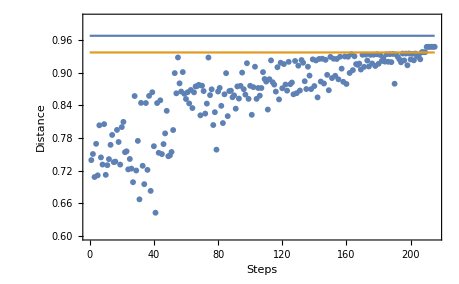

```mathematica
plot=ListPlot[Transpose[{Range[1,Length[data[[1]]]],data[[1]]}],PlotRange->{{0,Length[data[[1]]]},{0.6,1}},Axes->{False,False},Frame->True,FrameLabel->{"Steps","Distance"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->{460,Automatic},LabelStyle->{FontSize->18}];
plotQC=ListLinePlot[{{{0,DisQ},{Length[data[[1]]],DisQ}},{{0,DisC},{Length[data[[1]]],DisC}}}];
Show[plot,plotQC]
```